```mathematica
pars={bs->0.0001,b12->0.00012,ds->0.0001,d12->0.00012,b21->0.00012,d21->0.00012,s->2,V1->0.01,V2->0.01}
```

{bs→0.0001,b12→0.00012,ds→0.0001,d12→0.00012,b21→0.00012,d21→0.00012,s→2,V1→0.01,V2→0.01}

```mathematica
(* Does it matter whether we start above or below the expected ESS at the saddle? *)
(* Why do the traits not go to the expected NEEA? *)
```

```mathematica
(* What are the expected ESS values? *)Solve[D[(b1[t]-bs N1[t]-b12 N2[t])-(s b1[t]^2+ds N1[t]+d12 N2[t]),b1[t]]==0,b1[t]]/.pars
Solve[D[(b2[t]-bs N2[t]-b21 N1[t])-(s b2[t]^2+ds N2[t]+d21 N1[t]),b2[t]]==0,b2[t]]
```

{{b1[t]→1/4}}

{{b2[t]→1/(2 s)}}

```mathematica
Solve[Simplify[D[(b1[t]-bs N1[t]-b12 N2[t])/(s b1[t]^2+ds N1[t]+d12 N2[t]),b1[t]]]==0,b1[t]]
Solve[Simplify[D[(b2[t]-bs N2[t]-b21 N1[t])/(s b2[t]^2+ds N2[t]+d21 N1[t]),b2[t]]]==0,b2[t]]
```

NEEA1[t]=={{b1[t]→-(-2 bs s N1[t]-2 b12 s N2[t]+√(4 s (ds N1[t]+d12 N2[t])+(2 bs s N1[t]+2 b12 s N2[t])^2))/(2 s)},{b1[t]→(2 bs s N1[t]+2 b12 s N2[t]+√(4 s (ds N1[t]+d12 N2[t])+(2 bs s N1[t]+2 b12 s N2[t])^2))/(2 s)}}

NEEA2[t]=={{b2[t]→-(-2 b21 s N1[t]-2 bs s N2[t]+√(4 s (d21 N1[t]+ds N2[t])+(2 b21 s N1[t]+2 bs s N2[t])^2))/(2 s)},{b2[t]→(2 b21 s N1[t]+2 bs s N2[t]+√(4 s (d21 N1[t]+ds N2[t])+(2 b21 s N1[t]+2 bs s N2[t])^2))/(2 s)}}

```mathematica
(* When will the NEEA be larger than the ESS? *)
(2 b21 s N1[t]+2 bs s N2[t]+√(4 s (d21 N1[t]+ds N2[t])+(2 b21 s N1[t]+2 bs s N2[t])^2))/(2 s)>1/(2 s);
2 b21 s N1[t]+2 bs s N2[t]+√(4 s (d21 N1[t]+ds N2[t])+(2 b21 s N1[t]+2 bs s N2[t])^2)>1;
2 b21 s N1[t]+2 bs s N2[t]
```

```mathematica
soln=NDSolve[{N1'[t]==(b1[t]-bs N1[t]-b12 N2[t]) N1[t]-(s b1[t]^2+ds N1[t]+d12 N2[t])N1[t],
N2'[t]==(b2[t]-bs N2[t]-b21 N1[t]) N2[t]-(s b2[t]^2+ds N2[t]+d21 N1[t])N2[t],
b1'[t]==V1 (1-2 s b1[t]),
b2'[t]==V2 (1-2 s b2[t]),
N1[0]==50,N2[0]==25,b1[0]==.01,b2[0]==.01 }/.pars,{N1,N2,b1,b2},{t,0,1000}]
```

{{N1→InterpolatingFunction[{{0., 1000.}}, <>],N2→InterpolatingFunction[{{0., 1000.}}, <>],b1→InterpolatingFunction[{{0., 1000.}}, <>],b2→InterpolatingFunction[{{0., 1000.}}, <>]}}

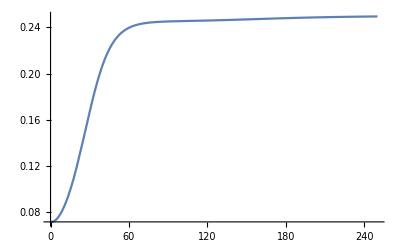

```mathematica
(* Plot how NEEA1 changes with changing population size *)
Plot[(2 bs s N1[t]+2 b12 s N2[t]+√(4 s (ds N1[t]+d12 N2[t])+(2 bs s N1[t]+2 b12 s N2[t])^2))/(2 s)/.pars/.soln, {t, 0,250},PlotRange->All]
```

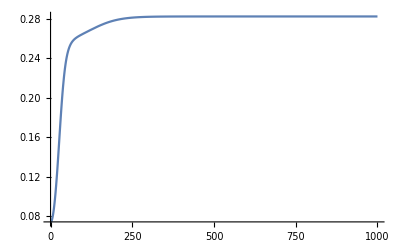

```mathematica
Plot[(2 b21 s N1[t]+2 bs s N2[t]+√(4 s (d21 N1[t]+ds N2[t])+(2 b21 s N1[t]+2 bs s N2[t])^2))/(2 s)/.pars/.soln,{t,0,1000},PlotRange->All]
```

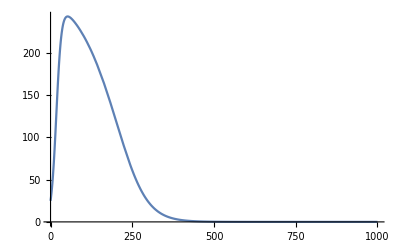

```mathematica
Plot[N2[t]/.soln,{t,0,1000}]
```